# Plots Maximum Metric Across Signals for epoch

## Data Selection

```mathematica
(*Set directory paths.*)
SetDirectory[NotebookDirectory[]];
plotsDir= "kl_div_plots";
dataDir = "mlflow_data";
bcRateKHz = 28608.8064;
```

```mathematica
(*Set the name of the experiment.*)
experiments =FileNameTake/@(FileNames[All, dataDir]);
experimentName =.;
PopupMenu[Dynamic[experimentName],experiments]
```

```mathematica
(*Select which metric to plot.*)
availableMetrics = {"kl", "reco", "loss","rate_0.3", "rate_1", "z_mean_squared_rate0.3", "loss_reco_full_rate0.3","loss_total_full_rate0.3", "loss_kl_full_rate0.3"};
desiredMetric=availableMetrics[[1]];
PopupMenu[Dynamic[desiredMetric, (desiredMetric=#;
SelectionMove[EvaluationNotebook[],Before,Notebook];
Do[NotebookFind[EvaluationNotebook[],tag,All,CellTags];
SelectionEvaluate[EvaluationNotebook[]],{tag,{"datasetSelection"}}])&
],availableMetrics]
desiredMetricPlotStyling = <|"kl"->"α × D_KL[𝒵 || 𝒩(0, 1)]", "reco"->"(1-α)×(𝒳 - 𝒳̂)^2", "loss"->"α × D_KL[𝒵 || 𝒩(0, 1)] + (1-α)×(𝒳 - 𝒳̂)^2", "z_mean_squared_rate0.3"->"TPR @ 10^-5 FPR (μ^2)", "loss_reco_full_rate0.3"->"TPR @ 10^-5 FPR (MSE)", "loss_total_full_rate0.3"->"TPR @ 10^-5 FPR (total)", "loss_kl_full_rate0.3"->"TPR @ 10^-5 FPR (KL)"|>;
```

```mathematica
(*get the experiment dir and runs*)
experimentDir=FileNameJoin[{dataDir,experimentName}];
runDirs=FileNames[All,experimentDir];
runNames=FileNameTake/@runDirs;

pathsByRun=<||>;
desiredRuns={};

DynamicModule[
{},
Column[
{
Style["Select one or more runs:",Bold],
CheckboxBar[
Dynamic[desiredRuns,(
desiredRuns=#;
pathsByRun=Association@Table[runName->Module[{runDir,files}, 
runDir=SelectFirst[runDirs,StringContainsQ[#,runName]&];
files=FileNames[All,runDir];
files=Select[files,StringContainsQ[#,desiredMetric<>"."]&];
files=Select[files,StringFreeQ[#,"test"]&];
If[StringContainsQ[desiredMetric,"rate"],DeleteCases[files,_?(StringContainsQ[#,"main_"]&)],files]
],{runName,desiredRuns}];
SelectionMove[EvaluationNotebook[],Before,Notebook];
Do[
NotebookFind[EvaluationNotebook[],tag,All,CellTags];
SelectionEvaluate[EvaluationNotebook[]],{tag,{"importData"}}
];
)&],runNames],
Dynamic[If[desiredRuns==={},"No runs selected.",Column[KeyValueMap[(*show only the count,not the full paths*)(#1<>": "<>ToString[Length[#2]]<>" files")&,pathsByRun]]]]
}
]
]
```

## Metadata

```mathematica
(*your helpers from above*)processDatasetNames[datasetName_]:=StringReplace[FileBaseName@Last@StringSplit[datasetName,"/"],RegularExpression["^(val_)?|(_loss.*|_rate.*|_cap.*|_z_mean_squared*|_loss_reco_full*|_loss_kl_full*)"]->""];
wrapLabel[label_,n_]:=StringJoin@Riffle[Partition[Characters[label],n,n,{1,1},""],"\n"];

selectedRun = "";
datasetNames = {};
DynamicModule[{},
Column[{Style["Pick one run:",Bold],
PopupMenu[Dynamic[selectedRun,
(
selectedRun=#;
datasetNames=processDatasetNames/@Lookup[pathsByRun,selectedRun,{}];
SelectionMove[EvaluationNotebook[],Before,Notebook];
Do[
NotebookFind[EvaluationNotebook[],tag,All,CellTags];
SelectionEvaluate[EvaluationNotebook[]],{tag,{"importData","plotGrid"}}
];
)&],
desiredRuns],
Dynamic[If[selectedRun===""||datasetNames==={},"⟨No datasets to display⟩",Framed[Pane[Column[datasetNames],{350,150},Scrollbars->True]]]]
}
]
]
```

## Import Data

```mathematica
(*Get the data to plot from all the runs inside the experiment.*)
plotData = Association[Table[runName ->Table[BinaryReadList[pathsByRun[runName][[i]], "Real32"], {i, 1, Length@pathsByRun[runName]}],{runName,Keys[pathsByRun] }]];
plotData[[selectedRun]] //Dimensions
```

{38,100}

```mathematica
(*Restrict values to be between 0 and 1, for better plotting visibility if the data is kl divergence related.*)
If[desiredMetric == "kl",plotData =Clip[plotData, {0,3}]];
If[desiredMetric == "loss",plotData =Clip[plotData, {0,5}]];
If[StringContainsQ[desiredMetric, "rate"], plotData = plotData/bcRateKHz];
```

```mathematica
Style["Plotting data for " <> selectedRun, "Title"]
```

Plotting data for scan_lr0.0005_alpha0.6

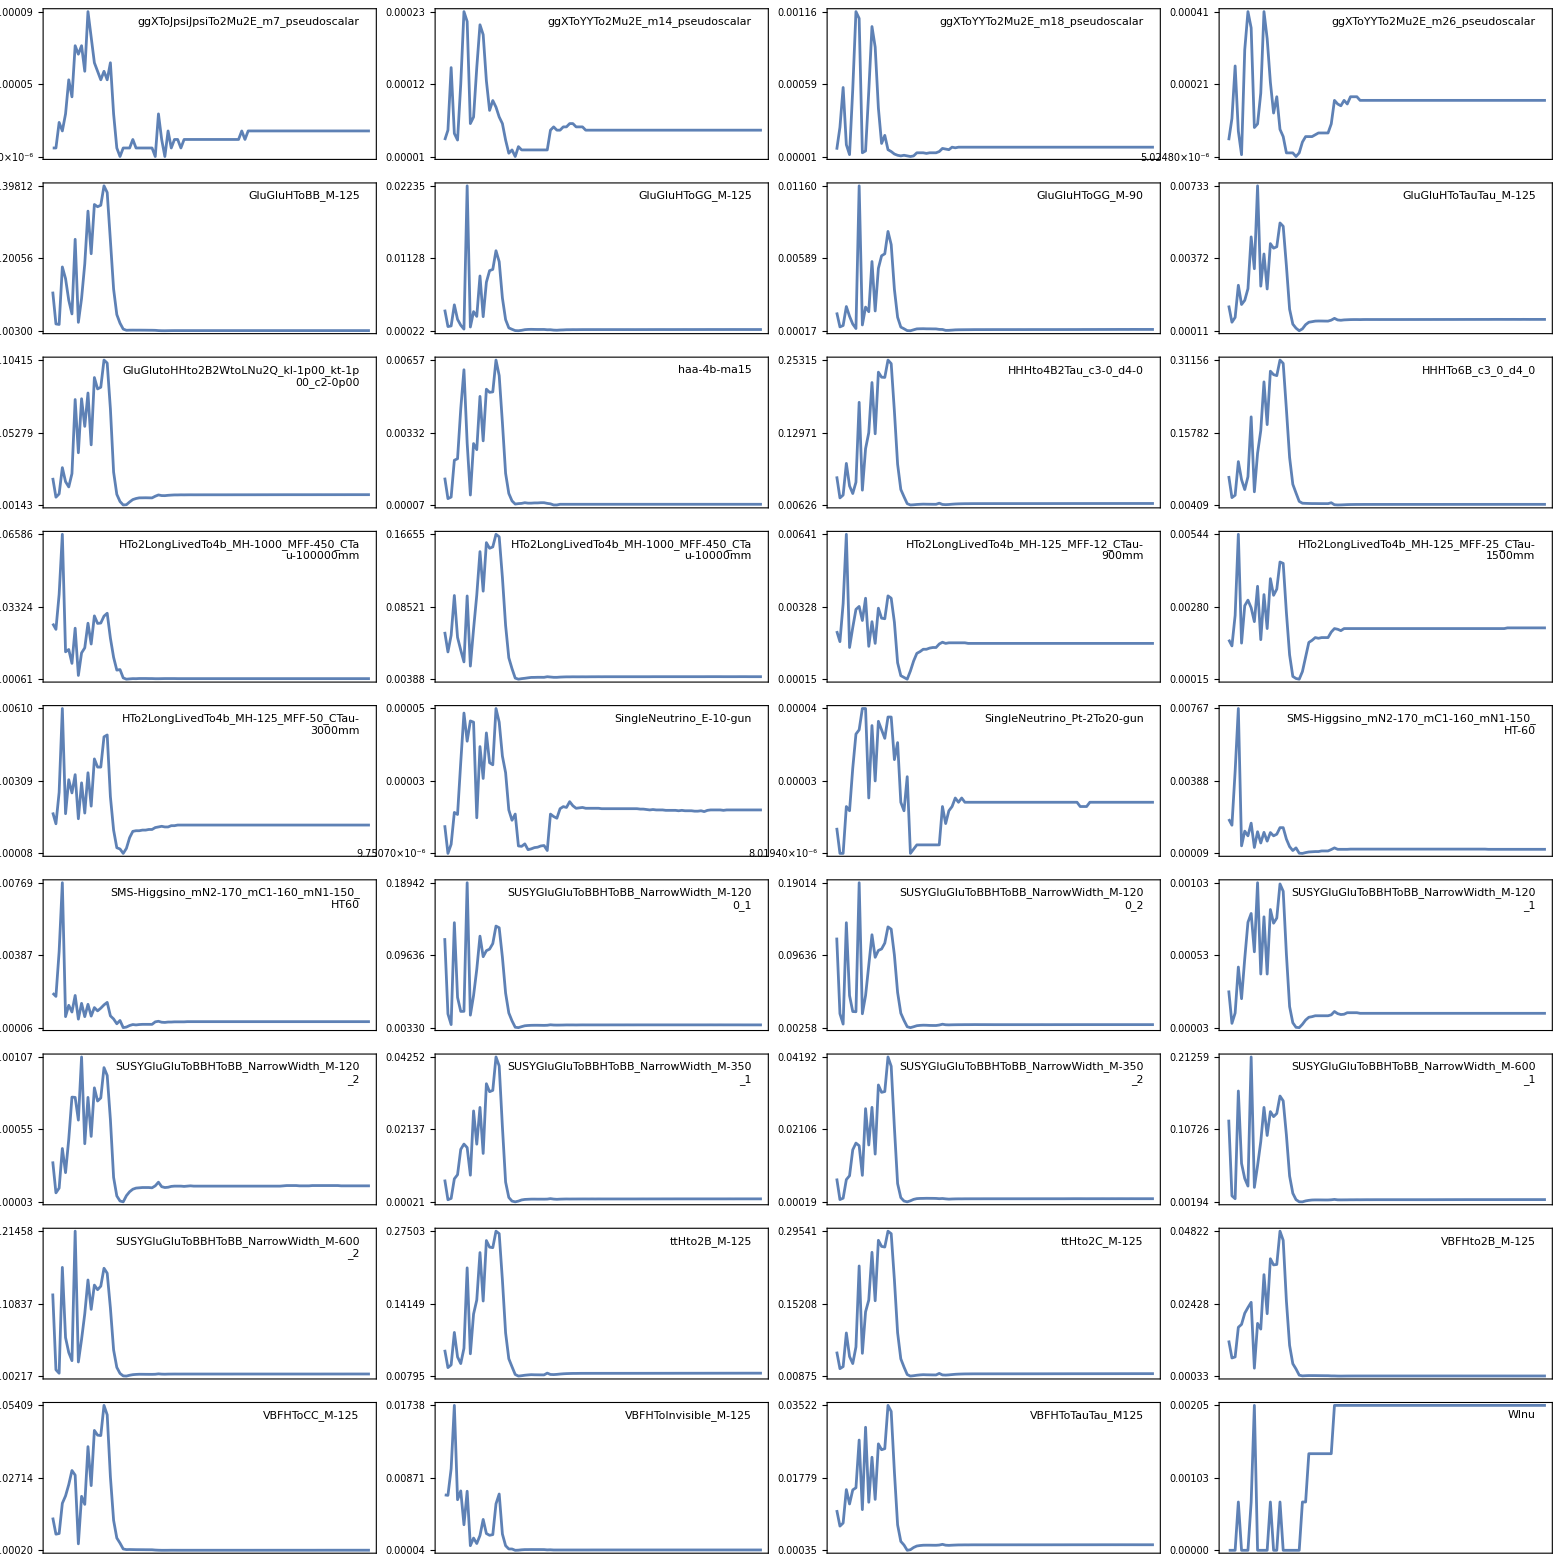
TPR @ 10^-5 FPR (KL) | -Graphics-
 | Epochs ∈ [0, 100]

```mathematica
selectedRunPlotData = plotData[selectedRun];
makePlot[row_,label_]:=ListLinePlot[
row,
PlotStyle->{Medium},
Axes->False,
Frame->True,
FrameTicks->
{
{
{
{Min[row],NumberForm[N[Min[row]],{5,5}]},
{(Min[row]+(Max[row] - Min[row])/2),NumberForm[N[Min[row]+(Max[row] - Min[row])/2],{5,5}]},
{Max[row],NumberForm[N[Max[row]],{5,5}]}},None
},
{None,None}
},
FrameTicksStyle->Directive[11,FontWeight->"Plain"],
PlotRange->{All, {Min[row], Max[row]}},
ImageSize->300,
PlotLabel->None,
Epilog->{Inset[Style[label,11,FontWeight->"Plain",Background->White],Scaled[{0.95,0.95}],{Right,Top}]}
]
datasetNamesWrapped=wrapLabel[#,37]&/@datasetNames;
plots=MapThread[makePlot,{selectedRunPlotData,datasetNamesWrapped}];

possiblePartitions = Divisors[Length@datasetNames];
plotsPerRow = possiblePartitions[[4]];
grid=Partition[plots,4];

fullGridWithAxes=Grid[{{"",Grid[grid,Spacings->{1,1},Alignment->Center]},{"",Style["Epochs ∈ [0, 100]",FontWeight->"SemiBold",24, Gray]}},Spacings->{1,2}];
Row[{Style[Rotate[desiredMetricPlotStyling[desiredMetric],90 Degree],FontWeight->"SemiBold",24, Gray],Spacer[10],fullGridWithAxes}]
```

```mathematica
Export["dataset_grids/" <>FileBaseName@desiredMetric <> "_" <>desiredRun <> ".png",%]
```

StringJoin::string: String expected at position 2 in dataset_grids/kl_<>desiredRun<>.png.

Export::chtype: First argument dataset_grids/kl_<>desiredRun<>.png is not a valid file specification.

$Failed

# Overall Plot

```mathematica
datasetPlotStyling=<|
"train"->"ZeroBias_train",
"ggXToJpsiJpsiTo2Mu2E_m7_pseudoscalar"->"gg → X_(7 GeV) → J/ψ J/ψ → (μ⁺μ⁻)(e⁺e⁻)",
"ggXToYYTo2Mu2E_m14_pseudoscalar"->"gg → X_(14 GeV) → YY → (μ⁺μ⁻)(e⁺e⁻)",
"ggXToYYTo2Mu2E_m18_pseudoscalar"->"gg → X_(18 GeV) → YY → (μ⁺μ⁻)(e⁺e⁻)",
"ggXToYYTo2Mu2E_m26_pseudoscalar"->"gg → X_(26 GeV) → YY → (μ⁺μ⁻)(e⁺e⁻)",
"GluGluHToBB_M-125"-> "gg → H(125 GeV) → bb̄",
"GluGluHToGG_M-125"-> "gg → H(125 GeV) → gg",
"GluGluHToGG_M-90"->"gg → H(90 GeV) → gg", 
"GluGluHToTauTau_M-125"-> "gg → H(125 GeV) → τ^+τ^-",
"GluGlutoHHto2B2WtoLNu2Q_kl-1p00_kt-1p00_c2-0p00"-> "gg → HH → bb̄W^+W^- → (l^±ν)(qq̄')",
"HHHto4B2Tau_c3-0_d4-0" -> "HHH → bb̄bb̄τ^+τ^-",
"HHHTo6B_c3_0_d4_0"->"HHH → 6b",
"HTo2LongLivedTo4b_MH-1000_MFF-450_CTau-100000mm"-> "H (10^3 GeV) → LL (10^3 mm) → 4b",
"HTo2LongLivedTo4b_MH-125_MFF-12_CTau-900mm" -> "H (125 GeV) → LL (900 mm) → 4b",
"HTo2LongLivedTo4b_MH-125_MFF-25_CTau-1500mm" ->"H (125 GeV) → LL (1500 mm) → 4b",
"HTo2LongLivedTo4b_MH-125_MFF-50_CTau-3000mm" -> "H (125 GeV) → LL (3000 mm) → 4b",
"haa-4b-ma15"->"H → AA → 4b", 
"VBFHto2B_M-125"->"VV → H → bb̄", 
"HTo2LongLivedTo4b_MH-1000_MFF-450_CTau-10000mm" -> "H (10^3 GeV) → 2LL (10^4 mm) → 4b", 
"main_val"->"ZeroBias",
"SingleNeutrino_E-10-gun" -> "Background Sim 1",
"SingleNeutrino_Pt-2To20-gun" -> "Background Sim 2",
"SMS-Higgsino_mN2-170_mC1-160_mN1-150_HT-60" -> "higgsino 1",
"SMS-Higgsino_mN2-170_mC1-160_mN1-150_HT60" ->"higgsino 2",
"SUSYGluGluToBBHToBB_NarrowWidth_M-1200_1" -> "gg → bb̄H(1200 GeV) → bb̄",
"SUSYGluGluToBBHToBB_NarrowWidth_M-1200_2" -> "gg → bb̄H(1200 GeV) → bb̄",
"SUSYGluGluToBBHToBB_NarrowWidth_M-120_1" -> "gg → bb̄H(120 GeV) → bb̄",
"SUSYGluGluToBBHToBB_NarrowWidth_M-120_2" -> "gg → bb̄H(120 GeV) → bb̄",
"SUSYGluGluToBBHToBB_NarrowWidth_M-350_1" -> "gg → bb̄H(350 GeV) → bb̄",
"SUSYGluGluToBBHToBB_NarrowWidth_M-350_2" -> "gg → bb̄H(350 GeV) → bb̄",
"SUSYGluGluToBBHToBB_NarrowWidth_M-600_1" -> "gg → bb̄H(600 GeV) → bb̄",
"SUSYGluGluToBBHToBB_NarrowWidth_M-600_2"-> "gg → bb̄H(600 GeV) → bb̄",
"ttHto2B_M-125" -> "tt̄ → H(125 GeV) → bb̄",
"ttHto2C_M-125" -> "tt̄ → H(125 GeV) → cc̄",
"VBFHToCC_M-125"->"VV → H → cc̄",
"VBFHToInvisible_M-125"->"VV → H → invis",
"VBFHToTauTau_M125"->"VV → H → τ^+τ^-",
"Wlnu" -> "W^± → l^±ν_l",
"WToTauTo3Mu" -> "W^± → τ^± → μ^±μ^+μ^-",
"WToTauToMuMuMu" -> "W^± → τ^± → μ^±μ^+μ^-"
|>;
labels = Style[#,FontSize->18, Italic]&/@(datasetPlotStyling/@datasetNames);



processRunName[runName_] := (
name = {};
splitRunName = StringSplit[runName,"_"];
lrName = Select[splitRunName, StringContainsQ["lr"]];
alphaName =Select[splitRunName, StringContainsQ["alpha"]];
name =Append[name, "ℓ = "<>Flatten@StringCases[lrName,NumberString] <> ", " <> "α = "<>Flatten@StringCases[alphaName,NumberString]];
name
)

(*Color function for selected lines*)
hexColors={"#3f90da","#ffa90e","#bd1f01","#94a4a2","#832db6","#a96b59","#e76300","#b9ac70","#717581","#92dadd"};
colorFunc=Function[i,RGBColor[hexColors[[Mod[i-1,Length[hexColors]]+1]]]];

(*Compute per-column means for each dataset in plotData*)
columnMeansData=KeyValueMap[Function[{key,mat},key->Module[{cols=Dimensions[mat][[2]]},Table[{j,Mean[mat[[All,j]]]},{j,cols}]]],plotData];
stdDevData=KeyValueMap[Function[{key,mat},key->Module[{cols=Dimensions[mat][[2]]},Table[StandardDeviation[mat[[All,j]]],{j,cols}]]],plotData];

(*Extract and scale series*)
series=Values[columnMeansData];
stdevSeries=Values[stdDevData]; 

(*Determine scaling for y-values:two significant figures*)
allYRaw=Flatten[series[[All,All,2]]];
scaleExp=Floor[Log10[Max[Abs[allYRaw]]]];
scaleFactor=10^scaleExp;

scaledSeries=Map[{#[[1]],#[[2]]/scaleFactor}&,series,{2}];
scaledStdevSeries=Map[#/scaleFactor&,stdevSeries,{2}]*10^-1; (*numeric mapping*)

(*Build shaded bands for standard deviation*)
bandGraphics=Table[Module[{meanPts=scaledSeries[[i]],sdVals=scaledStdevSeries[[i]],upper,lower},upper=MapThread[{#1[[1]],#1[[2]]+#2}&,{meanPts,sdVals}];
lower=MapThread[{#1[[1]],#1[[2]]-#2}&,{meanPts,sdVals}];
{colorFunc[i],Opacity[0.2],Polygon[Join[upper,Reverse[lower]]]}],{i,Length@scaledSeries}];

(*Legend labels*)
labelsKeysRaw=Keys[columnMeansData];
labelsKeys=Flatten[processRunName/@labelsKeysRaw];

(*X-axis ticks:major every 5,minor every 1*)
numCols=Length@First@series;
majorLen=Scaled[0.015];
minorLen=Scaled[0.015/2];
majorPositions=Range[1,numCols,5];
majorTicks=Table[{i,i,{majorLen,0}},{i,majorPositions}];
minorPositions=Complement[Range[1,numCols],majorPositions];
minorTicks=Table[{i,"",{minorLen,0}},{i,minorPositions}];
xTicks=Join[majorTicks,minorTicks];
xTicksUpper=xTicks/. {v_,_,len_}:>{v,"",len};

(*Y-axis ticks:5 intervals on scaled data,formatted to 2 significant figures*)
allY=Flatten[scaledSeries[[All,All,2]]];
yMin=Min[allY];
yMax=Max[allY];
yStep=(yMax-yMin)/5;
(*Major Y-ticks*)
majorPositionsY=Table[yMin+i*yStep,{i,0,5}];
majorTicksY=Table[{pos,NumberForm[pos,{3,2}],{majorLen,0}},{pos,majorPositionsY}];
(*Minor Y-ticks:5 between majors*)
minorTicksY=Flatten[Table[Table[{majorPositionsY[[k]]+j*(yStep/6),"",{minorLen,0}},{j,1,5}],{k,1,Length[majorPositionsY]-1}],1];
(*Combined Y-ticks*)
yTicks=Join[majorTicksY,minorTicksY];
yTicksRight=yTicks/. {v_,_,len_}:>{v,"",len};

cmsText=Row[{Style["CMS",Bold,FontFamily->"TeX Gyre Heros",24],Style[" Simulation Preliminary",Italic,FontFamily->"TeX Gyre Heros",24]}];
tevText = Row[{Style["14 TeV",FontFamily->"TeX Gyre Heros",24],""}];

(*Plot*)
plt =ListLinePlot[
scaledSeries,
Prolog->bandGraphics,
Joined->True,
Axes->False,
Frame->True,
FrameTicks->{{yTicks,yTicksRight},{xTicks,xTicksUpper}},FrameLabel->{Style["Epoch",Black,FontSize->30,FontFamily->"TeX Gyre Heros"],Style[Row[{"Mean " <> desiredMetricPlotStyling[desiredMetric] <>" ×",Superscript[10,scaleExp]}],Black,FontSize->30,FontFamily->"TeX Gyre Heros"]},PlotStyle->(colorFunc/@Range[Length@series]),
PlotLegends->Placed[SwatchLegend[labelsKeys,LegendMarkerSize->15,LabelStyle->Directive[Black,FontSize->26,FontFamily->"TeX Gyre Heros"]],Scaled[{0.84,0.83}]],
LabelStyle->Directive[Black,FontSize->28,FontFamily->"TeX Gyre Heros"],
FrameTicksStyle->Directive[AbsoluteThickness[2]],
Epilog->{Text[Style["σ_plot = σ × 10^-1",Black,FontSize->26,FontFamily->"TeX Gyre Heros"],Scaled[{0.85,0.2}]]},
PlotRangePadding->{{Scaled[0.011],Scaled[0.02]},{Scaled[0.04],Scaled[0.12]}},
ImageSize->1300,
AspectRatio->0.5
];

outer=Graphics[{Inset[plt,Scaled[{0,0}],{Left,Bottom},Scaled[1]],Inset[cmsText,Scaled[{0.082,0.94}],{Left,Bottom},Scaled[1]], Inset[tevText,Scaled[{0.81,0.95}],{Left,Bottom},Scaled[1]] },PlotRange->{{0,1},{0,1}}, AspectRatio->0.5, ImageSize->1300]
```

-Graphics-

```mathematica
Export["final_presentation_plots/" <>"mean_value_" <> desiredMetric <>"_lr0.0001.pdf",outer]
```

final_presentation_plots/mean_value_loss_kl_full_rate0.3_lr0.0001.pdf

```mathematica
Export["final_presentation_plots/" <>"mean_value_" <> desiredMetric <>"_lr0.001.pdf",outer]
```

final_presentation_plots/mean_value_loss_kl_full_rate0.3_lr0.001.pdf

```mathematica
Export["final_presentation_plots/" <>"mean_value_" <> desiredMetric <>"_alpha0.6.pdf",outer]
```

final_presentation_plots/mean_value_loss_kl_full_rate0.3_alpha0.6.pdf